Do the following tasks using Mathematica.
∫∫_R (x^2−xy+y^2)dA , where R is the region bounded by the ellipse x^2−xy+y^2 = 2. Use the transformation: x = √2  u - √(2/3)v , y =√2  u + √(2/3)  v

(a) Plot R in both xy and uv planes.

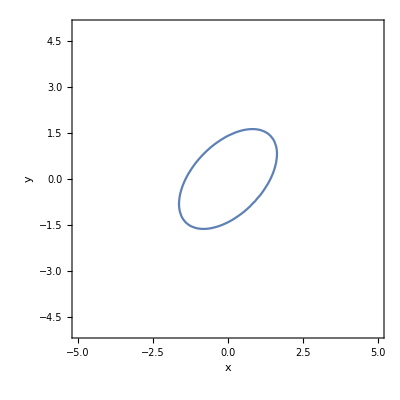

```mathematica
ContourPlot[x^2-x y+y^2==2,{x,-5,5},{y,-5,5},Axes-> True,AxesLabel->Automatic]
```

```mathematica
x = √2  u - √(2/3)  v ;
y = √2  u + √(2/3)  v ;
```

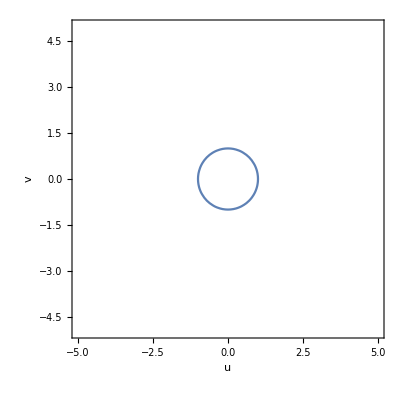

```mathematica
ContourPlot[x^2-x y+y^2==2,{u,-5,5},{v,-5,5},Axes-> True,AxesLabel->Automatic]
```

(b) Find the Jacobian of the transformation

```mathematica
jac = Det[D[{x,y},{{u,v}}]]
```

4/(√3)

(c) Evaluate the integral using the transformation

```mathematica
Solve[{x^2-x y+y^2==2},{v}]
```

{{v→-√(1-u^2)},{v→√(1-u^2)}}

```mathematica
∫_-1^1 ∫_(-√(1-u^2))^(√(1-u^2)) (x^2-x y+y^2)(jac)ⅆvⅆu
```

(4 π)/(√3)